# Functions

## Don’t need them but need to change options of Plot, ListPlot...

```mathematica
Needs["Fitting`"]
$HistoryLength=1;
Needs["MaTeX`"]
```

```mathematica
SetDirectory["/Users/hyunwoooh/Downloads/WS/hubbard-prudence/adiabatic"]
```

/Users/hyunwoooh/Downloads/WS/hubbard-prudence/adiabatic

## amplitude function

```mathematica
amp[t_]:=Norm[t]^2
```

# Full of my Code

```mathematica
AbsoluteTiming@Module[{dim=4,T=500,Tscale,H,Es,L,g,e,f,x,sol,ov,gapmax,Hinitial,Hend,timescale1=1,timescale2=1/√2.,Tscale1,aa,bb,evs,error,w,w2,w3,diffs, dt=0.01,pathc,qd,dt2=0.005},


H[t_]:=((Sin[t] 2.1+Sin[t √2])*Hinitial+(Cos[t] 2.7+Cos[t √2])*Hend);

Hinitial={{-0.978011,0.442537,-1.13173,-0.885678},{0.442537,-0.888185,-0.238622,0.40392},{-1.13173,-0.238622,1.04262,-0.563516},{-0.885678,0.40392,-0.563516,0.552724}};

Hend={{0.0482198,0.593326,-0.64427,0.680961},{0.593326,-0.00816359,-0.186093,-0.463839},{-0.64427,-0.186093,0.800334,0.700095},{0.680961,-0.463839,0.700095,0.545787}};

Es[t_]:=Sort[Eigenvalues[H[t]]];

(*
Print[Plot[Es[t],{t,0, T},PlotLegends->{"",""},
ImageSize->600,Frame->True,FrameStyle->BlackFrame,PlotLabel->MaTeX["\\text{}",FontSize->20],FrameLabel->{MaTeX["t",FontSize->20],MaTeX["\\text{Eigenvalues}",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All]];
*)
Print[Plot[{Es[t][[1]],Es[t][[2]],Es[t][[3]],Es[t][[4]]},{t,0,T},PlotLegends->{},
ImageSize->600,Frame->True,FrameStyle->BlackFrame,PlotLabel->MaTeX["\\text{}",FontSize->20],FrameLabel->{MaTeX["t",FontSize->20],MaTeX["\\Delta(t)",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All]];


Print[Plot[Es[t][[2]]-Es[t][[1]],{t,0,T},PlotLegends->{},
ImageSize->600,Frame->True,FrameStyle->BlackFrame,PlotLabel->MaTeX["\\text{}",FontSize->20],FrameLabel->{MaTeX["t",FontSize->20],MaTeX["\\Delta(t)",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All]];

g[t_]:=Module[{eig,vec,ord,r},
{eig,vec}=Eigensystem[H[t]];ord=Ordering[eig]; (*Eigenvecotr does not depend on T*)
Return [vec[[ord]][[1]]]
];

e[t_]:=Module[{eig,vec,ord,r},
{eig,vec}=Eigensystem[H[t]];ord=Ordering[eig]; (*Eigenvecotr does not depend on T*)
Return [vec[[ord]]]
];

evs={e[0]};
Print[AbsoluteTiming[For[i=1,i<=T /dt2,i++,
Module[{aaa={},states=e[i*dt2]},
For[j=1,j<=dim,j++,If[evs[[i,j]].states[[j]]<0,AppendTo[aaa,-states[[j]]],AppendTo[aaa,states[[j]]]]];
AppendTo[evs,aaa];
]
(*Print[et];*)
]]];

(*
diffs=Table[(evs[[100dt(t+1)+1,1]]-evs[[100dt t+1,1]])/dt,{t,0,T/dt-1}];

pathc=Norm/@diffs;

qd=Tscale Table[(dldt[[i]].(H[i dt]-Es[i dt][[1]]IdentityMatrix[dim]).dldt[[i]])/Norm[dldt[[i]]]^2,{i,1,T/dt}];*)


diffs=Table[(evs[[1./dt2*dt(t+1)+1,1]]-evs[[1./dt2*dt t+1,1]])/dt,{t,0,T/dt-1}];
pathc=Norm/@diffs;

qd=Table[(diffs[[i]].(H[i dt]-Es[i dt][[1]]IdentityMatrix[dim]).diffs[[i]])/Norm[diffs[[i]]]^2,{i,1,T/dt}];

Print[ListPlot[{Table[{t*dt,pathc[[t]]},{t,1,T/dt}]},
PlotLegends->Placed[LineLegend[{MaTeX["\\lVert | g'(t) \\rangle \\rVert"],MaTeX["\\int_0^t dt \\; \\lVert (1-|g(t)\\rangle \\langle g(t) | ) | g'(t) \\rangle \\rVert"]},LegendFunction->(Framed[Style[#]]&)],{Right,Bottom}],
ImageSize->600,Frame->True,FrameStyle->BlackFrame,PlotLabel->MaTeX["\\text{}",FontSize->20],FrameLabel->{MaTeX["t",FontSize->20],MaTeX["L(t)",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All]];

Print[ListPlot[{Table[{t*dt,dt Plus@@pathc[[;;t]]},{t,1,T/dt}]},
PlotLegends->Placed[LineLegend[{MaTeX["\\int_0^t dt \\; \\lVert | g'(t) \\rangle \\rVert"],MaTeX["\\int_0^t dt \\; \\lVert (1-|g(t)\\rangle \\langle g(t) | ) | g'(t) \\rangle \\rVert"]},LegendFunction->(Framed[Style[#]]&)],{Right,Bottom}],
ImageSize->600,Frame->True,FrameStyle->BlackFrame,PlotLabel->MaTeX["\\text{}",FontSize->20],FrameLabel->{MaTeX["t",FontSize->20],MaTeX["L(t)",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All]];

Print@(dt Plus@@pathc);



(*Print[Show[Plot[1000x,{x,0,time}],ListPlot[Table[{t*dt,Plus@@Table[(diffs[[i]].(H[i dt]-Es[i dt][[1]]IdentityMatrix[dim]).diffs[[i]])/Norm[diffs[[i]]]^2,{i,1,t}]},{t,1,time/dt}]],PlotLegends->{},
ImageSize->600,Frame->True,FrameStyle->BlackFrame,PlotLabel->MaTeX["\\text{}",FontSize->20],FrameLabel->{MaTeX["t",FontSize->20],MaTeX["Q_D(t) \\equiv \\int_0^{t} dt \\; \\frac{\\langle g'(t) |H| g'(t) \\rangle}{\\langle g'(t)|g'(t)\\rangle}",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All]];*)

(*Print[Table[(diffs[[i]].(H[i dt]-E[i dt][[1]]IdentityMatrix[dim]).diffs[[i]])/Norm[diffs[[i]]]^2,{i,1,time/dt}]];
Print[Table[Eigenvalues[(H[i dt]-E[i dt][[1]]IdentityMatrix[dim])],{i,1,time/dt}]];
Print[Table[{f[i dt],E[i dt][[1]]},{i,1,time/dt}]];*)



w={{0,20}};
Do[error=0;
Tscale=10w[[-1,2]];
While[error<0.005,
sol=NDSolveValue[{I x'[t]== Tscale H[t].x[t],x[0]==g[0]},x,{t,0,z},AccuracyGoal->10, PrecisionGoal->10(*,WorkingPrecision->10,MaxSteps->Infinity*)];
(*Print[sol[T]];
Print[Norm[sol[0.01]-g[0.01]]];*)
(*Print@Plot[amp[sol[t]],{t,0,T},PlotLegends->{},
ImageSize->600,Frame->True,FrameStyle->BlackFrame,PlotLabel->MaTeX["T_\\text{scale}="<>ToString@Tscale,FontSize->20],FrameLabel->{MaTeX["t",FontSize->20],MaTeX["\\lVert | \\psi(t) \\rangle \\rVert",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All];*)

error=1.-amp[sol[z].g[z]]/amp[sol[z]];
If[error<=0.005, Tscale*=0.99]
(*
gapmax=Max[Table[Es[t][[2]]-Es[t][[1]],{t,0,T,0.01}]];
Print@Plot[{amp[sol[t].g[t]]/amp[sol[t]],(Es[t][[2]]-Es[t][[1]])/gapmax},{t,0,T},
PlotLegends->Placed[LineLegend[{MaTeX["|\\langle g(t) | \\psi(t) \\rangle|^2"],MaTeX["\\Delta(t)/\\Delta_\\text{max}"]},LegendFunction->(Framed[Style[#]]&)],{Right,Top}],
ImageSize->600,Frame->True,FrameStyle->BlackFrame,PlotLabel->MaTeX["T_\\text{scale}="<>ToString@Tscale,FontSize->20],FrameLabel->{MaTeX["t",FontSize->20],MaTeX["|\\langle g(t) | \\psi(t) \\rangle|^2 \\text{ / } \\Delta(t)/\\Delta_\\text{max}",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All];

]*)
];
AppendTo[w,{z,Tscale}];
,{z,5,T,5}];
w=Delete[w,1];
(*
w=Table[{z,
error=0.01;
While[error<0.005,
sol=NDSolveValue[{I x'[t]== Tscale H[t].x[t],x[0]==g[0]},x,{t,0,z},AccuracyGoal->10, PrecisionGoal->10(*,WorkingPrecision->10,MaxSteps->Infinity*)];
(*Print[sol[T]];
Print[Norm[sol[0.01]-g[0.01]]];*)
(*Print@Plot[amp[sol[t]],{t,0,T},PlotLegends->{},
ImageSize->600,Frame->True,FrameStyle->BlackFrame,PlotLabel->MaTeX["T_\\text{scale}="<>ToString@Tscale,FontSize->20],FrameLabel->{MaTeX["t",FontSize->20],MaTeX["\\lVert | \\psi(t) \\rangle \\rVert",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All];*)

error=1.-amp[sol[z].g[z]]/amp[sol[z]];
If[error<=0.005, Tscale*=0.98]
(*
gapmax=Max[Table[Es[t][[2]]-Es[t][[1]],{t,0,T,0.01}]];
Print@Plot[{amp[sol[t].g[t]]/amp[sol[t]],(Es[t][[2]]-Es[t][[1]])/gapmax},{t,0,T},
PlotLegends->Placed[LineLegend[{MaTeX["|\\langle g(t) | \\psi(t) \\rangle|^2"],MaTeX["\\Delta(t)/\\Delta_\\text{max}"]},LegendFunction->(Framed[Style[#]]&)],{Right,Top}],
ImageSize->600,Frame->True,FrameStyle->BlackFrame,PlotLabel->MaTeX["T_\\text{scale}="<>ToString@Tscale,FontSize->20],FrameLabel->{MaTeX["t",FontSize->20],MaTeX["|\\langle g(t) | \\psi(t) \\rangle|^2 \\text{ / } \\Delta(t)/\\Delta_\\text{max}",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All];

]*)
];Tscale},{z,5,T,5}];*)
w2=Table[{z,dt Plus@@pathc[[;;z/dt]]},{z,5,T,5}];
w3=Table[{z,w[[z/5,2]]dt Plus@@qd[[;;z/dt]]},{z,5,T,5}];


Print@ListPlot[w,PlotRange->All,ImageSize->600,Frame->True,FrameStyle->BlackFrame,FrameLabel->{MaTeX["t \\propto L",FontSize->20],MaTeX["T_{\\rm scale}",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All];
Print@ListPlot[w2,PlotRange->All,ImageSize->600,Frame->True,FrameStyle->BlackFrame,FrameLabel->{MaTeX["t",FontSize->20],MaTeX["L",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All];
Print@ListPlot[w3,PlotRange->All,ImageSize->600,Frame->True,FrameStyle->BlackFrame,FrameLabel->{MaTeX["t",FontSize->20],MaTeX["Q_D",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All];
Print@ListPlot[MapThread[{#1[[2]],#2[[2]]}&,{w2,w3}],PlotRange->All,ImageSize->600,Frame->True,FrameStyle->BlackFrame,FrameLabel->{MaTeX["L",FontSize->20],MaTeX["Q_D",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All];

]
```

# Check with Veronica

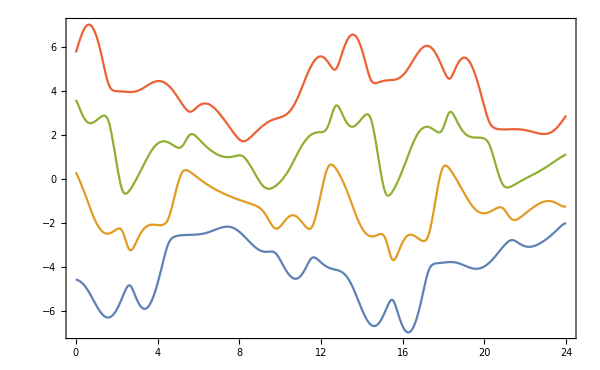

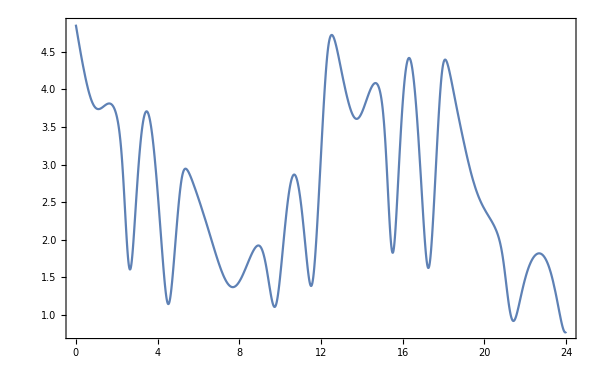

{0.193539,Null}

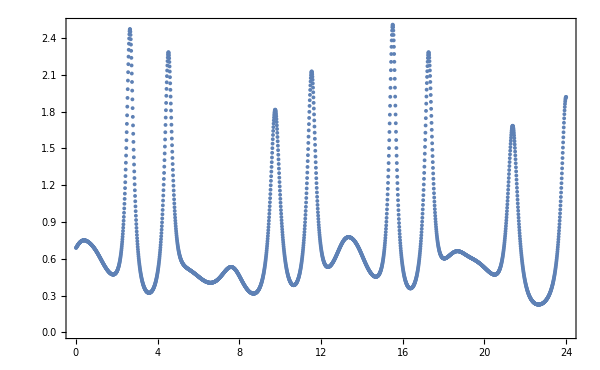

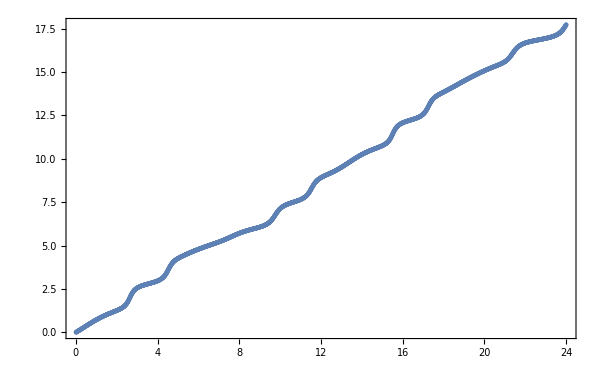

17.7266

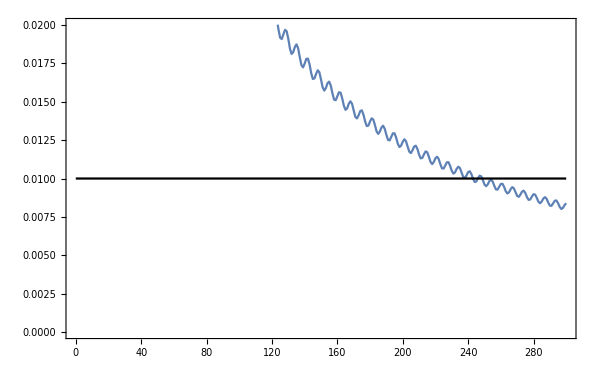

{141.713,Null}

```mathematica
AbsoluteTiming@Module[{dim=4,T=24,Tscale=10,H,Es,L,g,e,f,x,sol,ov,gapmax,Hinitial,Hend,timescale1=1,timescale2=1/√2.,Tscale1,aa,bb,evs,error,w,w2,w3,diffs, dt=0.01,pathc,qd,dt2=0.005},


H[t_]:=((Sin[t] 2.1+Sin[t √2])*Hinitial+(Cos[t] 2.7+Cos[t √2])*Hend);

Hinitial={{-0.978011,0.442537,-1.13173,-0.885678},{0.442537,-0.888185,-0.238622,0.40392},{-1.13173,-0.238622,1.04262,-0.563516},{-0.885678,0.40392,-0.563516,0.552724}};

Hend={{0.0482198,0.593326,-0.64427,0.680961},{0.593326,-0.00816359,-0.186093,-0.463839},{-0.64427,-0.186093,0.800334,0.700095},{0.680961,-0.463839,0.700095,0.545787}};

Es[t_]:=Sort[Eigenvalues[H[t]]];

(*
Print[Plot[Es[t],{t,0, T},PlotLegends->{"",""},
ImageSize->600,Frame->True,FrameStyle->BlackFrame,PlotLabel->MaTeX["\\text{}",FontSize->20],FrameLabel->{MaTeX["t",FontSize->20],MaTeX["\\text{Eigenvalues}",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All]];
*)
Print[Plot[{Es[t][[1]],Es[t][[2]],Es[t][[3]],Es[t][[4]]},{t,0,T},PlotLegends->{},
ImageSize->600,Frame->True,FrameStyle->BlackFrame,PlotLabel->MaTeX["\\text{}",FontSize->20],FrameLabel->{MaTeX["t",FontSize->20],MaTeX["\\Delta(t)",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All]];


Print[Plot[Es[t][[2]]-Es[t][[1]],{t,0,T},PlotLegends->{},
ImageSize->600,Frame->True,FrameStyle->BlackFrame,PlotLabel->MaTeX["\\text{}",FontSize->20],FrameLabel->{MaTeX["t",FontSize->20],MaTeX["\\Delta(t)",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All]];

g[t_]:=Module[{eig,vec,ord,r},
{eig,vec}=Eigensystem[H[t]];ord=Ordering[eig]; (*Eigenvecotr does not depend on T*)
Return [vec[[ord]][[1]]]
];

e[t_]:=Module[{eig,vec,ord,r},
{eig,vec}=Eigensystem[H[t]];ord=Ordering[eig]; (*Eigenvecotr does not depend on T*)
Return [vec[[ord]]]
];

evs={e[0]};
Print[AbsoluteTiming[For[i=1,i<=T /dt2,i++,
Module[{aaa={},states=e[i*dt2]},
For[j=1,j<=dim,j++,If[evs[[i,j]].states[[j]]<0,AppendTo[aaa,-states[[j]]],AppendTo[aaa,states[[j]]]]];
AppendTo[evs,aaa];
]
(*Print[et];*)
]]];

(*
diffs=Table[(evs[[100dt(t+1)+1,1]]-evs[[100dt t+1,1]])/dt,{t,0,T/dt-1}];

pathc=Norm/@diffs;

qd=Tscale Table[(dldt[[i]].(H[i dt]-Es[i dt][[1]]IdentityMatrix[dim]).dldt[[i]])/Norm[dldt[[i]]]^2,{i,1,T/dt}];*)


diffs=Table[(evs[[1./dt2*dt(t+1)+1,1]]-evs[[1./dt2*dt t+1,1]])/dt,{t,0,T/dt-1}];
pathc=Norm/@diffs;

qd=Table[(diffs[[i]].(H[i dt]-Es[i dt][[1]]IdentityMatrix[dim]).diffs[[i]])/Norm[diffs[[i]]]^2,{i,1,T/dt}];

Print[ListPlot[{Table[{t*dt,pathc[[t]]},{t,1,T/dt}]},
PlotLegends->Placed[LineLegend[{MaTeX["\\lVert | g'(t) \\rangle \\rVert"],MaTeX["\\int_0^t dt \\; \\lVert (1-|g(t)\\rangle \\langle g(t) | ) | g'(t) \\rangle \\rVert"]},LegendFunction->(Framed[Style[#]]&)],{Right,Bottom}],
ImageSize->600,Frame->True,FrameStyle->BlackFrame,PlotLabel->MaTeX["\\text{}",FontSize->20],FrameLabel->{MaTeX["t",FontSize->20],MaTeX["L(t)",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All]];

Print[ListPlot[{Table[{t*dt,dt Plus@@pathc[[;;t]]},{t,1,T/dt}]},
PlotLegends->Placed[LineLegend[{MaTeX["\\int_0^t dt \\; \\lVert | g'(t) \\rangle \\rVert"],MaTeX["\\int_0^t dt \\; \\lVert (1-|g(t)\\rangle \\langle g(t) | ) | g'(t) \\rangle \\rVert"]},LegendFunction->(Framed[Style[#]]&)],{Right,Bottom}],
ImageSize->600,Frame->True,FrameStyle->BlackFrame,PlotLabel->MaTeX["\\text{}",FontSize->20],FrameLabel->{MaTeX["t",FontSize->20],MaTeX["L(t)",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All]];

Print@(dt Plus@@pathc);



(*Print[Show[Plot[1000x,{x,0,time}],ListPlot[Table[{t*dt,Plus@@Table[(diffs[[i]].(H[i dt]-Es[i dt][[1]]IdentityMatrix[dim]).diffs[[i]])/Norm[diffs[[i]]]^2,{i,1,t}]},{t,1,time/dt}]],PlotLegends->{},
ImageSize->600,Frame->True,FrameStyle->BlackFrame,PlotLabel->MaTeX["\\text{}",FontSize->20],FrameLabel->{MaTeX["t",FontSize->20],MaTeX["Q_D(t) \\equiv \\int_0^{t} dt \\; \\frac{\\langle g'(t) |H| g'(t) \\rangle}{\\langle g'(t)|g'(t)\\rangle}",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All]];*)

(*Print[Table[(diffs[[i]].(H[i dt]-E[i dt][[1]]IdentityMatrix[dim]).diffs[[i]])/Norm[diffs[[i]]]^2,{i,1,time/dt}]];
Print[Table[Eigenvalues[(H[i dt]-E[i dt][[1]]IdentityMatrix[dim])],{i,1,time/dt}]];
Print[Table[{f[i dt],E[i dt][[1]]},{i,1,time/dt}]];*)

w=Table[{z,
sol=NDSolveValue[{I x'[t]== z H[t].x[t],x[0]==g[0]},x,{t,0,T},AccuracyGoal->10, PrecisionGoal->10(*,WorkingPrecision->10,MaxSteps->Infinity*)];
√(1.-amp[sol[T].g[T]]/amp[sol[T]])
}
,{z,1,300}];


(*
w2=Table[{z,dt Plus@@pathc[[;;z/dt]]},{z,24,T,5}];
w3=Table[{z,w[[z/5,2]]dt Plus@@qd[[;;z/dt]]},{z,24,T,5}];
*)

Print@ListLinePlot[w,ImageSize->600,Frame->True,FrameStyle->BlackFrame,Epilog->Plot[0.01,{x,0,300},PlotStyle->Black][[1]],FrameLabel->{MaTeX["t \\propto L",FontSize->20],MaTeX["\\epsilon",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->{All,{0,0.020}}];
(*
Print@ListPlot[w2,PlotRange->All,ImageSize->600,Frame->True,FrameStyle->BlackFrame,FrameLabel->{MaTeX["t",FontSize->20],MaTeX["L",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All];
Print@ListPlot[w3,PlotRange->All,ImageSize->600,Frame->True,FrameStyle->BlackFrame,FrameLabel->{MaTeX["t",FontSize->20],MaTeX["Q_D",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All];
Print@ListPlot[MapThread[{#1[[2]],#2[[2]]}&,{w2,w3}],PlotRange->All,ImageSize->600,Frame->True,FrameStyle->BlackFrame,FrameLabel->{MaTeX["L",FontSize->20],MaTeX["Q_D",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All];
*)
]
```

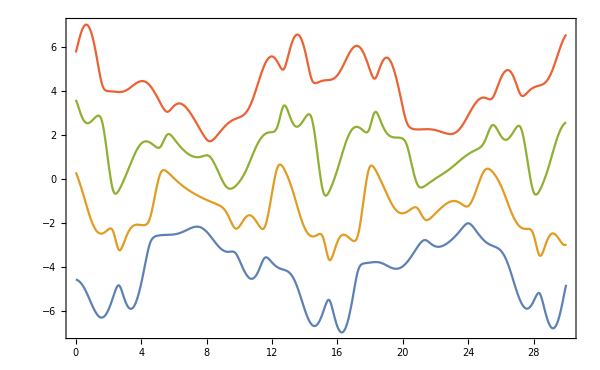

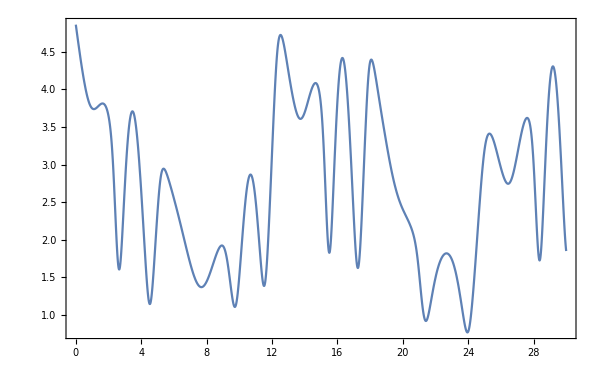

{0.257542,Null}

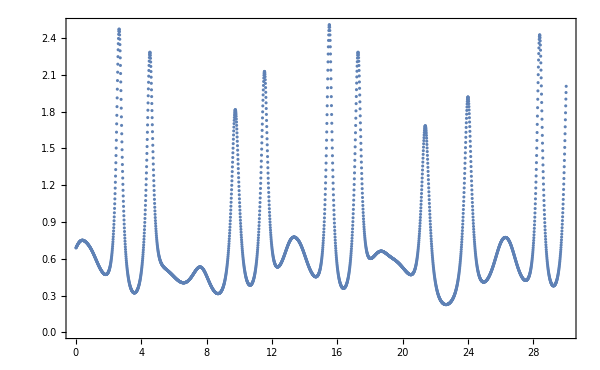

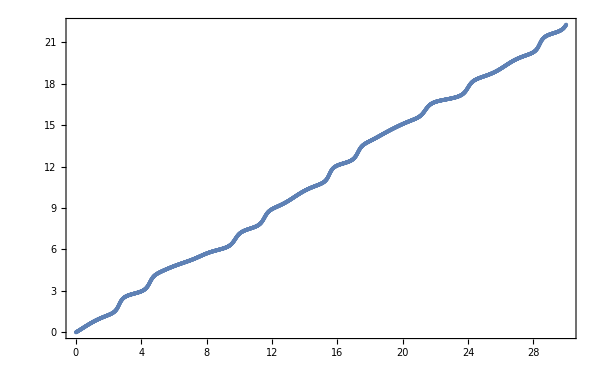

22.2615

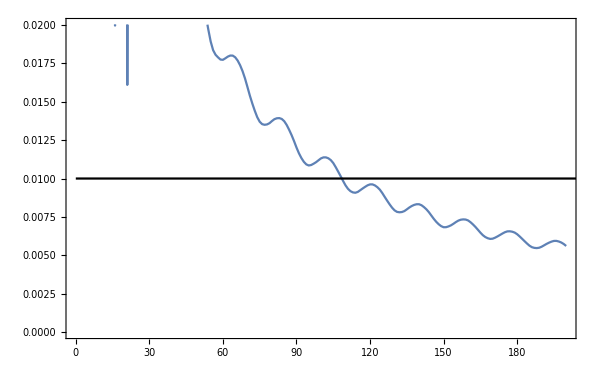

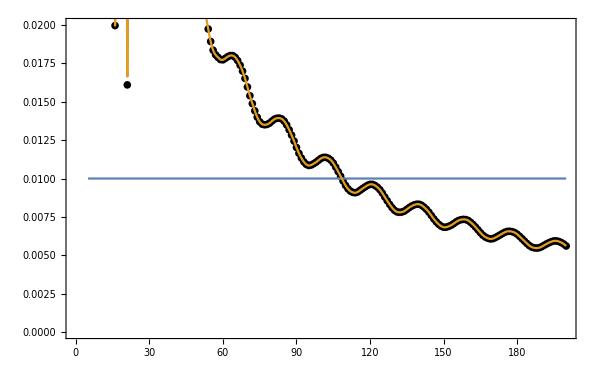

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{a→InverseFunction[InterpolatingFunction[…],1,1][0.01]}}

InterpolatingFunction::dmval: Input value {-6.42632} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.257368} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.628684} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{a→16.}

0.0199396

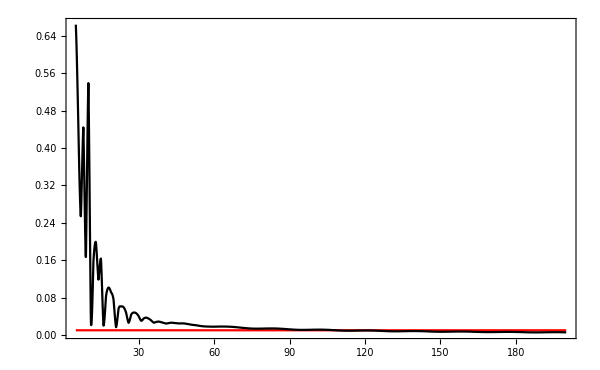

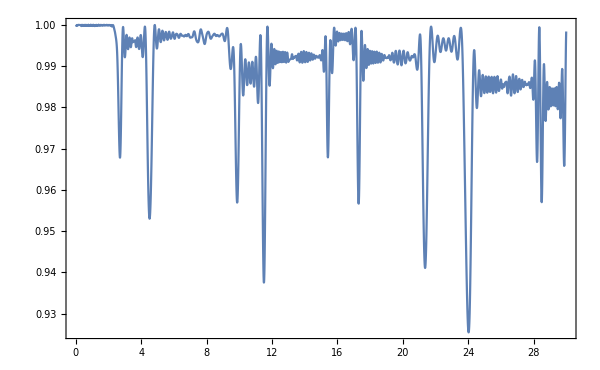

0.00165702

{{30,10.5541}}

{82.4249,Null}

```mathematica
AbsoluteTiming@Module[{dim=4,T=30,Tscale=10,H,Es,L,g,e,f,x,sol,ov,gapmax,Hinitial,Hend,timescale1=1,timescale2=1/√2.,Tscale1,aa,bb,evs,error,w,w2,w3,diffs, dt=0.01,pathc,qd,dt2=0.005,ww},


H[t_]:=((Sin[t] 2.1+Sin[t √2])*Hinitial+(Cos[t] 2.7+Cos[t √2])*Hend);

Hinitial={{-0.978011,0.442537,-1.13173,-0.885678},{0.442537,-0.888185,-0.238622,0.40392},{-1.13173,-0.238622,1.04262,-0.563516},{-0.885678,0.40392,-0.563516,0.552724}};

Hend={{0.0482198,0.593326,-0.64427,0.680961},{0.593326,-0.00816359,-0.186093,-0.463839},{-0.64427,-0.186093,0.800334,0.700095},{0.680961,-0.463839,0.700095,0.545787}};

Es[t_]:=Sort[Eigenvalues[H[t]]];

(*
Print[Plot[Es[t],{t,0, T},PlotLegends->{"",""},
ImageSize->600,Frame->True,FrameStyle->BlackFrame,PlotLabel->MaTeX["\\text{}",FontSize->20],FrameLabel->{MaTeX["t",FontSize->20],MaTeX["\\text{Eigenvalues}",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All]];
*)
Print[Plot[{Es[t][[1]],Es[t][[2]],Es[t][[3]],Es[t][[4]]},{t,0,T},PlotLegends->{},
ImageSize->600,Frame->True,FrameStyle->BlackFrame,PlotLabel->MaTeX["\\text{}",FontSize->20],FrameLabel->{MaTeX["t",FontSize->20],MaTeX["\\Delta(t)",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All]];


Print[Plot[Es[t][[2]]-Es[t][[1]],{t,0,T},PlotLegends->{},
ImageSize->600,Frame->True,FrameStyle->BlackFrame,PlotLabel->MaTeX["\\text{}",FontSize->20],FrameLabel->{MaTeX["t",FontSize->20],MaTeX["\\Delta(t)",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All]];

g[t_]:=Module[{eig,vec,ord,r},
{eig,vec}=Eigensystem[H[t]];ord=Ordering[eig]; (*Eigenvecotr does not depend on T*)
Return [Normalize@vec[[ord]][[1]]]
];

e[t_]:=Module[{eig,vec,ord,r},
{eig,vec}=Eigensystem[H[t]];ord=Ordering[eig]; (*Eigenvecotr does not depend on T*)
Return [Normalize/@vec[[ord]]]
];

evs={e[0]};
Print[AbsoluteTiming[For[i=1,i<=T /dt2,i++,
Module[{aaa={},states=e[i*dt2]},
For[j=1,j<=dim,j++,If[evs[[i,j]].states[[j]]<0,AppendTo[aaa,-states[[j]]],AppendTo[aaa,states[[j]]]]];
AppendTo[evs,aaa];
]
(*Print[et];*)
]]];

(*
diffs=Table[(evs[[100dt(t+1)+1,1]]-evs[[100dt t+1,1]])/dt,{t,0,T/dt-1}];

pathc=Norm/@diffs;

qd=Tscale Table[(dldt[[i]].(H[i dt]-Es[i dt][[1]]IdentityMatrix[dim]).dldt[[i]])/Norm[dldt[[i]]]^2,{i,1,T/dt}];*)


diffs=Table[(evs[[1./dt2*dt(t+1)+1,1]]-evs[[1./dt2*dt t+1,1]])/dt,{t,0,T/dt-1}];
pathc=Norm/@diffs;

qd=Table[(diffs[[i]].(H[i dt]-Es[i dt][[1]]IdentityMatrix[dim]).diffs[[i]])/Norm[diffs[[i]]]^2,{i,1,T/dt}];

Print[ListPlot[{Table[{t*dt,pathc[[t]]},{t,1,T/dt}]},
PlotLegends->Placed[LineLegend[{MaTeX["\\lVert | g'(t) \\rangle \\rVert"],MaTeX["\\int_0^t dt \\; \\lVert (1-|g(t)\\rangle \\langle g(t) | ) | g'(t) \\rangle \\rVert"]},LegendFunction->(Framed[Style[#]]&)],{Right,Bottom}],
ImageSize->600,Frame->True,FrameStyle->BlackFrame,PlotLabel->MaTeX["\\text{}",FontSize->20],FrameLabel->{MaTeX["t",FontSize->20],MaTeX["L(t)",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All]];

Print[ListPlot[{Table[{t*dt,dt Plus@@pathc[[;;t]]},{t,1,T/dt}]},
PlotLegends->Placed[LineLegend[{MaTeX["\\int_0^t dt \\; \\lVert | g'(t) \\rangle \\rVert"],MaTeX["\\int_0^t dt \\; \\lVert (1-|g(t)\\rangle \\langle g(t) | ) | g'(t) \\rangle \\rVert"]},LegendFunction->(Framed[Style[#]]&)],{Right,Bottom}],
ImageSize->600,Frame->True,FrameStyle->BlackFrame,PlotLabel->MaTeX["\\text{}",FontSize->20],FrameLabel->{MaTeX["t",FontSize->20],MaTeX["L(t)",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All]];

Print@(dt Plus@@pathc);



(*Print[Show[Plot[1000x,{x,0,time}],ListPlot[Table[{t*dt,Plus@@Table[(diffs[[i]].(H[i dt]-Es[i dt][[1]]IdentityMatrix[dim]).diffs[[i]])/Norm[diffs[[i]]]^2,{i,1,t}]},{t,1,time/dt}]],PlotLegends->{},
ImageSize->600,Frame->True,FrameStyle->BlackFrame,PlotLabel->MaTeX["\\text{}",FontSize->20],FrameLabel->{MaTeX["t",FontSize->20],MaTeX["Q_D(t) \\equiv \\int_0^{t} dt \\; \\frac{\\langle g'(t) |H| g'(t) \\rangle}{\\langle g'(t)|g'(t)\\rangle}",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All]];*)

(*Print[Table[(diffs[[i]].(H[i dt]-E[i dt][[1]]IdentityMatrix[dim]).diffs[[i]])/Norm[diffs[[i]]]^2,{i,1,time/dt}]];
Print[Table[Eigenvalues[(H[i dt]-E[i dt][[1]]IdentityMatrix[dim])],{i,1,time/dt}]];
Print[Table[{f[i dt],E[i dt][[1]]},{i,1,time/dt}]];*)

w=Table[{z,
sol=NDSolveValue[{I x'[t]== z H[t].x[t],x[0]==g[0]},x,{t,0,T},AccuracyGoal->10, PrecisionGoal->10(*,WorkingPrecision->10,MaxSteps->Infinity*)];
√(1.-amp[sol[T].g[T]]/amp[sol[T]])
}
,{z,1,200}];


(*
w2=Table[{z,dt Plus@@pathc[[;;z/dt]]},{z,24,T,5}];
w3=Table[{z,w[[z/5,2]]dt Plus@@qd[[;;z/dt]]},{z,24,T,5}];
*)

Print@ListLinePlot[w,ImageSize->600,Frame->True,FrameStyle->BlackFrame,Epilog->Plot[0.01,{x,0,300},PlotStyle->Black][[1]],FrameLabel->{MaTeX["t \\propto L",FontSize->20],MaTeX["\\epsilon",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->{All,{0,0.020}}];

Print@ListPlot[w,Epilog->Plot[{0.01,Interpolation[w][x]},{x,5,200}][[1]],ImageSize->600,Frame->True,FrameStyle->BlackFrame,PlotStyle->{Red,Black},FrameLabel->{MaTeX["t \\propto L",FontSize->20],MaTeX["\\epsilon",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->{All,{0,0.020}}];

Print[NSolve[Interpolation[w][a]==0.01,a]];
Print[FindRoot[Interpolation[w][a]==0.01,{a,1}]];
Print[Interpolation[w][15.999999999999988]];
Print@Plot[{0.01,Interpolation[w][x]},{x,5,200},ImageSize->600,Frame->True,FrameStyle->BlackFrame,PlotStyle->{Red,Black},FrameLabel->{MaTeX["t \\propto L",FontSize->20],MaTeX["\\epsilon",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All];

ww=Table[{z,
error=0.01;Tscale=1;
While[error>0.005,
sol=NDSolveValue[{I x'[t]== Tscale H[t].x[t],x[0]==g[0]},x,{t,0,z},AccuracyGoal->10, PrecisionGoal->10(*,WorkingPrecision->10,MaxSteps->Infinity*)];
(*Print[sol[T]];
Print[Norm[sol[0.01]-g[0.01]]];*)

error=1.-amp[sol[z].g[z]]/amp[sol[z]];
If[error>0.005, Tscale*=1.02]
(*
gapmax=Max[Table[Es[t][[2]]-Es[t][[1]],{t,0,T,0.01}]];
Print@Plot[{amp[sol[t].g[t]]/amp[sol[t]],(Es[t][[2]]-Es[t][[1]])/gapmax},{t,0,T},
PlotLegends->Placed[LineLegend[{MaTeX["|\\langle g(t) | \\psi(t) \\rangle|^2"],MaTeX["\\Delta(t)/\\Delta_\\text{max}"]},LegendFunction->(Framed[Style[#]]&)],{Right,Top}],
ImageSize->600,Frame->True,FrameStyle->BlackFrame,PlotLabel->MaTeX["T_\\text{scale}="<>ToString@Tscale,FontSize->20],FrameLabel->{MaTeX["t",FontSize->20],MaTeX["|\\langle g(t) | \\psi(t) \\rangle|^2 \\text{ / } \\Delta(t)/\\Delta_\\text{max}",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All];

]*)

];Print@Plot[amp[sol[t].g[t]]/amp[sol[t]],{t,0,T},PlotLegends->{},
ImageSize->600,Frame->True,FrameStyle->BlackFrame,PlotLabel->MaTeX["T_\\text{scale}="<>ToString@Tscale,FontSize->20],FrameLabel->{MaTeX["t",FontSize->20],MaTeX["\\lVert | \\psi(t) \\rangle \\rVert",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All];
Print[1.-amp[sol[T].g[T]]/amp[sol[T]]];
Tscale},{z,30,T,30}];
Print[ww]
(*
Print@ListPlot[w2,PlotRange->All,ImageSize->600,Frame->True,FrameStyle->BlackFrame,FrameLabel->{MaTeX["t",FontSize->20],MaTeX["L",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All];
Print@ListPlot[w3,PlotRange->All,ImageSize->600,Frame->True,FrameStyle->BlackFrame,FrameLabel->{MaTeX["t",FontSize->20],MaTeX["Q_D",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All];
Print@ListPlot[MapThread[{#1[[2]],#2[[2]]}&,{w2,w3}],PlotRange->All,ImageSize->600,Frame->True,FrameStyle->BlackFrame,FrameLabel->{MaTeX["L",FontSize->20],MaTeX["Q_D",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All];
*)
]
```

## check Q_D

My T is your T_end

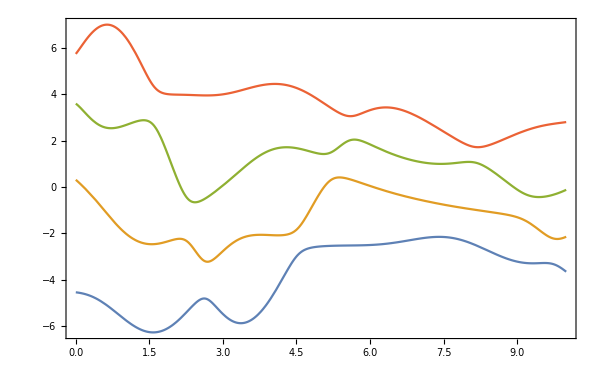

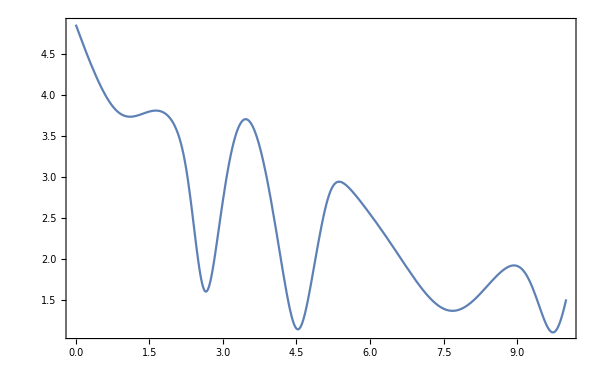

{0.075719,Null}

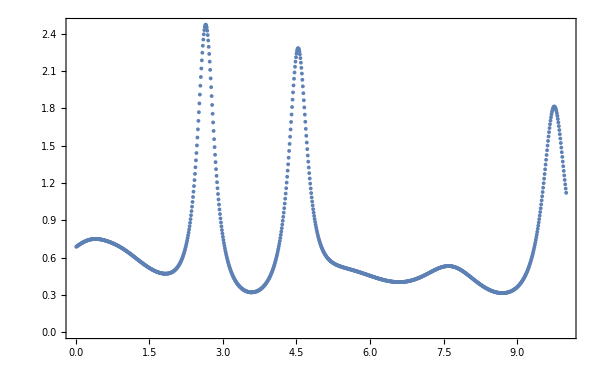

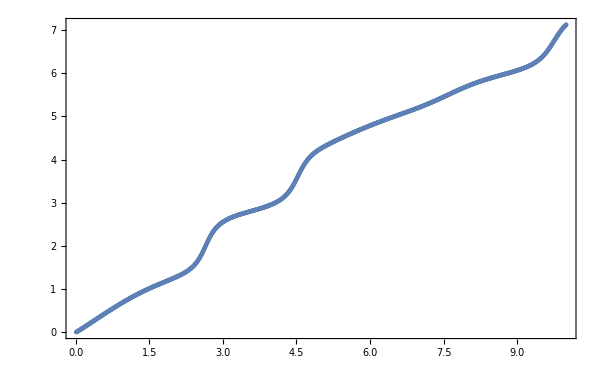

7.12629

{2.68717,4182.05}

```mathematica
AbsoluteTiming@Module[{dim=4,T=10,Tscale=100,H,Es,L,g,e,f,x,sol,ov,gapmax,Hinitial,Hend,timescale1=1,timescale2=1/√2.,Tscale1,aa,bb,evs,error,w,w2,w3,diffs, dt=0.01,pathc,qd,dt2=0.005},


H[t_]:=((Sin[t] 2.1+Sin[t √2])*Hinitial+(Cos[t] 2.7+Cos[t √2])*Hend);



Hinitial={{-0.978011,0.442537,-1.13173,-0.885678},{0.442537,-0.888185,-0.238622,0.40392},{-1.13173,-0.238622,1.04262,-0.563516},{-0.885678,0.40392,-0.563516,0.552724}};

Hend={{0.0482198,0.593326,-0.64427,0.680961},{0.593326,-0.00816359,-0.186093,-0.463839},{-0.64427,-0.186093,0.800334,0.700095},{0.680961,-0.463839,0.700095,0.545787}};

Es[t_]:=Sort[Eigenvalues[H[t]]];

(*Energy plot*)
Print[Plot[{Es[t][[1]],Es[t][[2]],Es[t][[3]],Es[t][[4]]},{t,0,T},PlotLegends->{},
ImageSize->600,Frame->True,FrameStyle->BlackFrame,PlotLabel->MaTeX["\\text{}",FontSize->20],FrameLabel->{MaTeX["t",FontSize->20],MaTeX["\\Delta(t)",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All]];

(*gap plot*)
Print[Plot[Es[t][[2]]-Es[t][[1]],{t,0,T},PlotLegends->{},
ImageSize->600,Frame->True,FrameStyle->BlackFrame,PlotLabel->MaTeX["\\text{}",FontSize->20],FrameLabel->{MaTeX["t",FontSize->20],MaTeX["\\Delta(t)",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All]];

(*Ground state*)
g[t_]:=Module[{eig,vec,ord,r},
{eig,vec}=Eigensystem[H[t]];ord=Ordering[eig]; (*Eigenvector does not depend on T*)
Return [vec[[ord]][[1]]]
];

(*all eigenstates*)
e[t_]:=Module[{eig,vec,ord,r},
{eig,vec}=Eigensystem[H[t]];ord=Ordering[eig]; (*Eigenvector does not depend on T*)
Return [vec[[ord]]]
];

(*Making the sign of eigenstates by comparing it with previous states*)
evs={e[0]};
Print[AbsoluteTiming[For[i=1,i<=T /dt2,i++,
Module[{aaa={},states=e[i*dt2]},
For[j=1,j<=dim,j++,If[evs[[i,j]].states[[j]]<0,AppendTo[aaa,-states[[j]]],AppendTo[aaa,states[[j]]]]];
AppendTo[evs,aaa];
]
(*Print[et];*)
]]];



(*Calculate norm of |g'>*)
diffs=Table[(evs[[1./dt2*dt(t+1)+1,1]]-evs[[1./dt2*dt t+1,1]])/dt,{t,0,T/dt-1}];
pathc=Norm/@diffs;

(*Calculate Subscript[Q, d]*)

qd=Table[(diffs[[i]].(H[i dt]-Es[i dt][[1]]IdentityMatrix[dim]).diffs[[i]])/Norm[diffs[[i]]]^2,{i,1,T/dt}];


(*Plot norm of |g'>*)
Print[ListPlot[{Table[{t*dt,pathc[[t]]},{t,1,T/dt}]},
PlotLegends->Placed[LineLegend[{MaTeX["\\lVert | g'(t) \\rangle \\rVert"],MaTeX["\\int_0^t dt \\; \\lVert (1-|g(t)\\rangle \\langle g(t) | ) | g'(t) \\rangle \\rVert"]},LegendFunction->(Framed[Style[#]]&)],{Right,Bottom}],
ImageSize->600,Frame->True,FrameStyle->BlackFrame,PlotLabel->MaTeX["\\text{}",FontSize->20],FrameLabel->{MaTeX["t",FontSize->20],MaTeX["L(t)",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All]];

(*Plot path length*)
Print[ListPlot[{Table[{t*dt,dt Plus@@pathc[[;;t]]},{t,1,T/dt}]},
PlotLegends->Placed[LineLegend[{MaTeX["\\int_0^t dt \\; \\lVert | g'(t) \\rangle \\rVert"],MaTeX["\\int_0^t dt \\; \\lVert (1-|g(t)\\rangle \\langle g(t) | ) | g'(t) \\rangle \\rVert"]},LegendFunction->(Framed[Style[#]]&)],{Right,Bottom}],
ImageSize->600,Frame->True,FrameStyle->BlackFrame,PlotLabel->MaTeX["\\text{}",FontSize->20],FrameLabel->{MaTeX["t",FontSize->20],MaTeX["L(t)",FontSize->20]},BaseStyle->{FontSize->20,FontFamily->"CMU Bright"},PlotRange->All]];

(*Print path length*)
Print@(dt Plus@@pathc);

(*Print Subscript[Q, D]*)
Tscale dt Plus@@qd
]
```